## Matrices and Quantum Operations

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Matrix multiplication

Tensor product

Unitary matrix

### Matrix Multiplication

You have just seen that quantum states can be represented as vectors and matrices. It should then be no surprise that quantum operators can also be represented this way. Matrix multiplication can be used to write down the rules by which a quantum operation turns one quantum state into another.

If you would like a full review of matrices and matrix arithmetic, this can be found in Introduction to Linear Algebra or Introduction to Finite Mathematics. Luckily, the Wolfram Language can automate the arithmetic so you can focus on the results.

Recall that a matrix can be specified as a list of lists:

```mathematica
{{a,b},{c,d}}//MatrixForm//TraditionalForm
```

(a | b
c | d)

A vector can be simply specified as a list of coefficients:

```mathematica
{x,y}//MatrixForm//TraditionalForm
```

(x
y)

The usual matrix product can be input using the Dot symbol:

```mathematica
{{a,b},{c,d}}.{x,y}
```

{a x+b y,c x+d y}

Written in traditional notation:

```mathematica
({{a, b}, {c, d}}).({{x}, {y}})//MatrixForm//TraditionalForm
```

(a x+b y
c x+d y)

#### Example

Compute the product of the matrix (2 | -5
-1 | 4) and the vector (3
-2).

##### Solution

Automate the computation:

```mathematica
{{2,-5},{-1,4}}.{3,-2}
```

{16,-11}

The product is the vector (16
-11).

### Quantum Operators as Matrices

Let’s examine the Dirac notation for the result of applying a particular quantum operator to an initial state:

```mathematica
(QuantumOperator[{{a,b},{c,d}}]@QuantumState[{x,y}])//TraditionalForm
```

(a x+b y)0+(c x+d y)1

This result should remind you of the generic matrix product in the last section.

```mathematica
(QuantumOperator[{{a,b},{c,d}}]@QuantumState[{x,y}])["Matrix"]//MatrixForm//TraditionalForm
```

(a x+b y
c x+d y)

You know from the last lesson that a quantum state can be represented by a list of amplitudes. These amplitudes can also represent coefficients in a complex vector space. Notice how the operator in the last example was specified by a 2×2 matrix.

All of the quantum gates you have seen in circuits can be represented by matrices. Below are some common qubit operations along with their circuit diagram symbols and matrices in the computational basis:

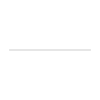
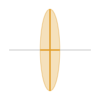
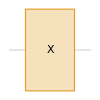
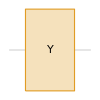
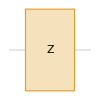
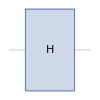
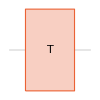
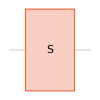
Operator | Diagram | Matrix
I | -Graphics- | (1 | 0
0 | 1)
NOT | -Graphics- | (0 | 1
1 | 0)
X | -Graphics- | (0 | 1
1 | 0)
Y | -Graphics- | (0 | -ⅈ
ⅈ | 0)
Z | -Graphics- | (1 | 0
0 | -1)
H | -Graphics- | (1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
T | -Graphics- | (1 | 0
0 | ⅇ^((ⅈ π)/4))
S | -Graphics- | (1 | 0
0 | ⅈ)
P[θ] | -Graphics- | (1 | 0
0 | ⅇ^(ⅈ θ))

```mathematica
With[{operators={"I","NOT","X","Y","Z","H","T","S","P"[θ]}},
Style[Grid[Prepend[Table[{Style[op,Bold],QuantumCircuitOperator[{op}]["Diagram",ImageSize->{100,100},"WireLabels"->None],TraditionalForm@MatrixForm@QuantumOperator[op]["Matrix"]},{op,operators}],Map[Style[#,"Subsubsection"]&,{"Operator","Diagram","Matrix"}]],Spacings->{1, 2},Frame->All,Alignment->Center],"Text"]
]
```

### Circuits as Matrices

A quantum circuit is just the application of a sequence of quantum operations to your initial state. The matrix which represents the entire circuit is just the product of all the matrices representing the individual operations.

Consider the following example:

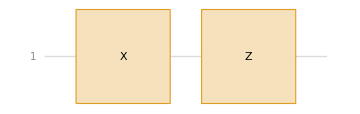

```mathematica
circuitXZ=QuantumCircuitOperator[{"X","Z"}];
circuitXZ["Diagram"]
```

The "Matrix" property of operators and circuit operators can be used to obtain their matrix representation:

```mathematica
circuitXZ["Matrix"]//MatrixForm//TraditionalForm
```

(0 | 1
-1 | 0)

Let’s check that the product of the operator’s matrices gives the circuit’s matrix:

```mathematica
(QuantumOperator["Z"]["Matrix"].QuantumOperator["X"]["Matrix"])//MatrixForm//TraditionalForm
```

(0 | 1
-1 | 0)

```mathematica
QuantumOperator["Z"]["Matrix"].QuantumOperator["X"]["Matrix"]==circuitXZ["Matrix"]
```

True

That means the result of running any given quantum circuit on any initial state can be classically computed by performing enough matrix multiplications:

```mathematica
(circuitXZ@QuantumState[{1/2,√3/2}])["Formula"]
```

(√3)/2 0-1/21

```mathematica
(circuitXZ@QuantumState[{1/2,√3/2}])["Matrix"]//MatrixForm//TraditionalForm
```

((√3)/2
-1/2)

```mathematica
(circuitXZ@QuantumState[{1/2,√3/2}])["Matrix"]==circuitXZ["Matrix"].QuantumState[{1/2,√3/2}]["Matrix"]
```

True

That’s essentially how the Wolfram Quantum Framework allows you to compute the results of running quantum circuits, even though it is a classical computer program. For small quantum circuits, you are far better just doing the matrix multiplications classically than trying to build and run a quantum computer. However, the size of the matrices needed to model quantum circuits grows exponentially with the number of qubits involved. Thus, classical computers eventually reach a limit on the size of quantum system which they can effectively predict.

### Multi-qubit States

So far, you have only seen matrix and vector representations of single qubits and single-qubit operations. However, a useful quantum circuit will have more than one qubit. How can these be represented with matrices?

Consider the 2-qubit state “10”. A 2-qubit state can be specified by 4 complex amplitudes:

```mathematica
QuantumState["10"]["Amplitudes"]
```

<|00→0,01→0,10→1,11→0|>

It is conventional to order the vector coefficients by ascending value of the basis bit sequences when read in binary:

```mathematica
QuantumState["10"]["Matrix"]//MatrixForm//TraditionalForm
```

(0
0
1
0)

In general, a 2-qubit state would look like this:

```mathematica
QuantumState[{a,b,c,d}]["Amplitudes"]
```

<|00→a,01→b,10→c,11→d|>

```mathematica
QuantumState[{a,b,c,d}]["Formula"]
```

a00+b01+c10+d11

```mathematica
QuantumState[{a,b,c,d}]["Matrix"]//MatrixForm//TraditionalForm
```

(a
b
c
d)

Also remember that it is conventional for the amplitudes to be normalized so that Norm[{a,b,c,d}]^2==1. However, this convention is not automatically enforced in the framework:

```mathematica
QuantumState[{a,b,c,d}]["Probabilities"]
```

<|00→Abs[a]^2/(Abs[a]^2+Abs[b]^2+Abs[c]^2+Abs[d]^2),01→Abs[b]^2/(Abs[a]^2+Abs[b]^2+Abs[c]^2+Abs[d]^2),10→Abs[c]^2/(Abs[a]^2+Abs[b]^2+Abs[c]^2+Abs[d]^2),11→Abs[d]^2/(Abs[a]^2+Abs[b]^2+Abs[c]^2+Abs[d]^2)|>

If the amplitudes are already normalized, then the probability of each measurement result is just the norm squared of each amplitude:

```mathematica
QuantumState[{a,b,c,d}]["Probabilities"]//Map[#/.Norm[{a,b,c,d}]^2->1&]
```

<|00→Abs[a]^2,01→Abs[b]^2,10→Abs[c]^2,11→Abs[d]^2|>

You should take note that each of the amplitudes above correspond to the combined 2-qubit state. What if you want to begin with two single-qubit states and describe their combination?

This can be represented with the mathematical operation of the tensor product. You can automate the computation of tensor products using the QuantumTensorProduct function:

```mathematica
combinedstate=QuantumTensorProduct[QuantumState[{a0,a1}],QuantumState[{b0,b1}]]
```

QuantumState[…]

Note how the amplitudes of the combined state are related to the products of amplitudes of the single-qubit states:

```mathematica
combinedstate["Formula"]
```

a0 b000+a0 b101+a1 b010+a1 b111

The probability distribution may look complicated at first:

```mathematica
combinedstate["Probabilities"]
```

<|00→Abs[a0 b0]^2/(Abs[a0 b0]^2+Abs[a1 b0]^2+Abs[a0 b1]^2+Abs[a1 b1]^2),01→Abs[a0 b1]^2/(Abs[a0 b0]^2+Abs[a1 b0]^2+Abs[a0 b1]^2+Abs[a1 b1]^2),10→Abs[a1 b0]^2/(Abs[a0 b0]^2+Abs[a1 b0]^2+Abs[a0 b1]^2+Abs[a1 b1]^2),11→Abs[a1 b1]^2/(Abs[a0 b0]^2+Abs[a1 b0]^2+Abs[a0 b1]^2+Abs[a1 b1]^2)|>

However, the expression simplifies greatly if the amplitudes of each single qubit state were properly normalized:

```mathematica
combinedstate["Probabilities"]//Map[FullSimplify[#,Norm[{a0,a1}]^2 Norm[{b0,b1}]^2==1]&]
```

<|00→Abs[a0 b0]^2,01→Abs[a0 b1]^2,10→Abs[a1 b0]^2,11→Abs[a1 b1]^2|>

#### Example

Suppose qubit 1 is in the state ψ_1=1 and qubit 2 is in the state ψ_2=3/5 0+4/5 1.

Represent their combined state as a vector. Compute the probability for each possible bit sequence if the combined state is measured in the computational basis.

##### Solution

The combined state will be a tensor product:

```mathematica
examplestate=QuantumTensorProduct[QuantumState[{0,1}],QuantumState[{3/5,4/5}]]
```

QuantumState[…]

The Dirac notation and amplitudes are as follows:

```mathematica
examplestate["Formula"]
```

3/5 10+4/5 11

```mathematica
examplestate["Amplitudes"]
```

<|00→0,01→0,10→3/5,11→4/5|>

This can be represented by the following vector:

```mathematica
examplestate["StateVector"]//Normal
```

{0,0,3/5,4/5}

Probabilities are the norm squared of the normalized amplitudes:

```mathematica
examplestate["Probabilities"]
```

<|00→0,01→0,10→9/25,11→16/25|>

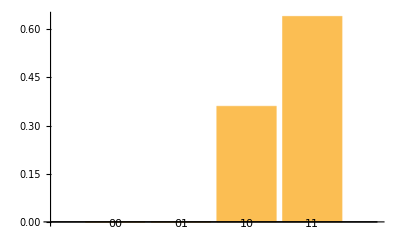

```mathematica
examplestate["ProbabilitiesPlot"]
```

### Multi-qubit Operators

Since much of quantum mechanics can be represented by linear algebra, matrix multiplication (and more generally tensor contraction) can be used to let classical computers predict the results of running quantum circuits. However, this is only practical up to a certain size of quantum system.

The state vector for an n-qubit state is of dimension 2^n. Operators that act on n-qubits must then be of size 2^n×2^n. Thus, while classical computers can simulate the same computations as digital quantum computers, this becomes exponentially harder as the size of the quantum computer grows.

The table below has some common 2-qubit operations along with their circuit diagrams and matrix representations in the computational basis:

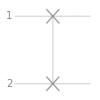
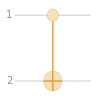
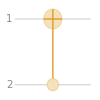
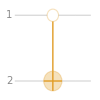
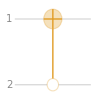
Operator | Diagram | Matrix
SWAP→{1,2} | -Graphics- | (1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)
CNOT→{1,2} | -Graphics- | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)
CNOT→{2,1} | -Graphics- | (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)
C0NOT→{1,2} | -Graphics- | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)
C0NOT→{2,1} | -Graphics- | (0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
With[{operators={"SWAP"->{1,2},"CNOT"->{1,2},"CNOT"->{2,1},"C0NOT"->{1,2},"C0NOT"->{2,1}}},
Style[Grid[Prepend[Table[{Style[op,Bold],QuantumCircuitOperator[{op}]["Diagram",ImageSize->{100,100}],TraditionalForm@MatrixForm@QuantumOperator[op]["Matrix"]},{op,operators}],Map[Style[#,"Subsubsection"]&,{"Operator","Diagram","Matrix"}]],Spacings->{1, 2},Frame->All,Alignment->Center],"Text"]
]
```

### Unitary Operators

You may wonder, can any matrix represent a quantum operation? According the usual formalism of quantum mechanics, the answer is a resounding no. Only a special class of matrices called unitary matrices can represent quantum operations.

A unitary matrix has the special mathematical property that U†=U^-1. In Wolfram Language, this is equivalent to ConjugateTranspose[U]==Inverse[U]. This also implies Abs(Det(U))=1, where Det computes the matrix determinant.

Consider the following operator:

```mathematica
U=QuantumOperator[{{4/5,3/5},{-3/5,4/5}},"Label"->"U"]
```

QuantumOperator[…]

This operator is specified by a unitary matrix:

```mathematica
U["UnitaryQ"]
```

True

```mathematica
Abs[Det[U["Matrix"]]]==1
```

True

User-defined operators can be used in circuit diagrams:

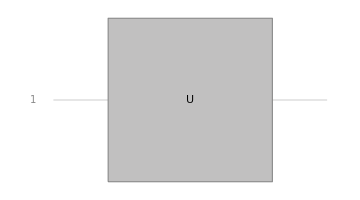

```mathematica
QuantumCircuitOperator[{U}]["Diagram"]
```

This particular unitary has the following effect on the register state:

```mathematica
QuantumCircuitOperator[{U}][]["Formula"]
```

4/5 0-3/51

```mathematica
QuantumCircuitOperator[{U}][]["BlochPlot",ImageSize->Small]
```

-Graphics3D-

Multi-qubit operators can be defined by matrices of the appropriate size:

```mathematica
V=QuantumOperator[{{1/2,-√3/2,0,0},{√3/2,1/2,0,0},{0,0,1,0},{0,0,0,1}},"Label"->"V"]
```

QuantumOperator[…]

```mathematica
V["UnitaryQ"]
```

True

Note that the following circuit automatically includes two qubits so that the operator V can act:

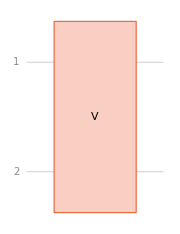

```mathematica
QuantumCircuitOperator[{V}]["Diagram",ImageSize->Small]
```

This circuit results in the following state:

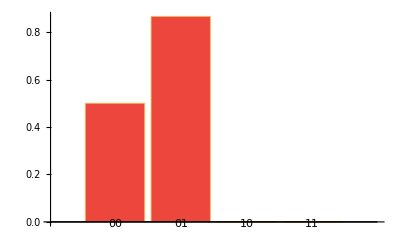

```mathematica
QuantumCircuitOperator[{V}][]["AmplitudesPlot",ChartLegends->Automatic]
```

In the following example circuit, you can apply the 1-qubit operation U to the second qubit and the 2-qubit operation V to the first and third qubits:

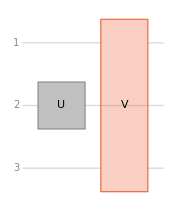

```mathematica
circuitUV=QuantumCircuitOperator[{U->2,V->{1,3}}];
circuitUV["Diagram",ImageSize->Small]
```

Correctly computing this circuit’s 8×8 matrix by hand would be tedious, but the computation can be automatically handled by the Wolfram Quantum Framework:

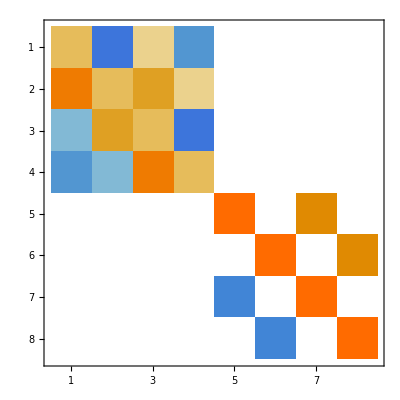

```mathematica
circuitUV["Matrix"]//MatrixPlot
```

Applying this circuit to the register state gives the following result:

```mathematica
circuitUV[]["Formula"]
```

2/5 000+(2 √3)/5 001-3/10010-(3 √3)/10011

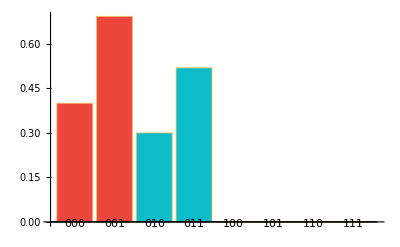

```mathematica
circuitUV[]["AmplitudesPlot",ChartLegends->Automatic]
```